# Simulations

## Parameters

```mathematica
ClearAll[cg,Vg,R, δlac, mE,y,ξunit, Nf, Nr];
cg=15.;(*"Millimolar" -> glc in feed*)
Vg=0.5;(*"Millimoles"/"Grams"/"Hours" -> max glc uptake*)
R=0.4; (*"Millimoles"/"Grams"/"Hours" -> max uptake of pyruvate by mitochondria (max. respiration)*)
δlac=0.0022/2;(*1/"Millimolar"/"Hours" -> lac death rate*)
mE=1;(*"Millimoles"/"Grams"/"Hours" -> maintenance ATP demand*)
y=QuantityMagnitude[1/UnitConvert[Quantity[0.24393939393939396,"Moles"/"Grams"],"Millimoles"/"Grams"]];
Nf = 2;(* stoichometric coeficient of fermentation *)
Nr = 19; (* stoichometric coeficient of respiration *)
{cg,Vg,R,y,δlac,mE}=Rationalize[{cg,Vg,R,y,δlac,mE}];
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[0.9,"Nanograms"]Quantity["Days"/"Milliliters"]);
```

## Functions

Polytope

```mathematica
ClearAll[vo,vl,vatpMaxGlobal,vatpMaxLocal,vatpMinGlobal,vatpMinLocal,vgMaxGlobal,vgMaxLocal,vgMinGlobal,vgMinLocal]
vo[vg_,vatp_]:=(vatp-Nf*vg)/Nr;
vl[vg_,vatp_]:=(vatp-Nf*vg*(1+Nr))/Nr;
vatpMinGlobal = vatpMinLocal[vgMinGlobal];
vatpMaxGlobal[ξ_]:=vatpMaxLocal[vgMaxGlobal[ξ]];
vatpMinLocal [vg_] := Nf*vg; 
vatpMaxLocal[vg_] := Min[Nf(1+Nr)vg,Nf*vg+Nr*R];

vgMinGlobal = 0;
vgMaxGlobal[ξ_] :=   Min[Vg,cg/ξ];
vgMinLocal[vatp_]:=Max[vatp/(Nf+Nr),vatp-Nr*R]/Nf;
vgMaxLocal[ξ_][vatp_]:=Min[vgMaxGlobal[ξ],vatp/Nf];

vertices[ξ_]:=If[vatpMaxGlobal[ξ]>19R,
{{0,0},{2vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]},{20R,R/2}},
{{0,0},{2vgMaxGlobal[ξ],vgMaxGlobal[ξ]},{vatpMaxGlobal[ξ],vgMaxGlobal[ξ]}}]

polytope[ξ_][vg_,vatp_]:=Boole[vatp/(Nf(1+Nr))≤vg≤vgMaxGlobal[ξ]∧Nf vg ≤ vatp ≤ Nr R + Nf vg];
```

Growth Functions

```mathematica
ClearAll[δ,λ,λmax]
δ[sg_,sl_]:=δlac sl;
λ[sg_,sl_][vg_,vatp_]:=y(vatp-mE)-δ[sg,sl];
λmax[sg_,sl_,ξ_]:=λ[sg,sl][0.,vatpMaxGlobal[ξ]]
```

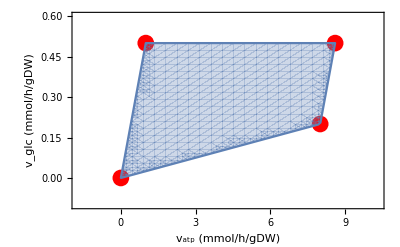

```mathematica
Module[{ξ=2},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-0.2 vatpMaxGlobal[ξ],1.2vatpMaxGlobal[ξ]},{-0.2vgMaxGlobal[ξ],1.2vgMaxGlobal[ξ]}},
FrameLabel->{"v_atp (mmol/h/gDW)","v_glc (mmol/h/gDW)"},Frame->True,PlotRange->{{0,10},{0,0.6}},Axes->False],
RegionPlot[polytope[ξ][vg,vatp]==1,{vatp,vatpMinGlobal,vatpMaxGlobal[ξ]},{vg,vgMinGlobal,vgMaxGlobal[ξ]}]]]
```

Partition, expected values, variances, covariances

```mathematica
ClearAll[generateIntegral];

(* The integral in all the polytope *) 
generateIntegral[fun_,β_,ξ_,{atplb_,atpub_},{glbf_,gubf_}]:=Module[{int0,int1,lb,ub},
int1=Simplify@Integrate[Exp[-β y(vatpMaxGlobal[ξ]-vatp)]fun[vg,vatp],
{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
int0=Simplify@Integrate[fun[vg,vatp],{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
Piecewise[{{0, atplb≥atpub}, {int1, β>0}, {int0, β==0}}]];
```

```mathematica
generateIntegral[1][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{0,Min[20R,2vgMaxGlobal[ξ]]},{{ξ,vatp}↦vatp/40,{ξ,vatp}↦vatp/2}];
generateIntegral[2][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{2vgMaxGlobal[ξ],Min[20R,vatpmax[ξ]]},{{ξ,vatp}↦vatp/40,{ξ,vatp}↦Mg[ξ]}];
generateIntegral[3][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{20R,2Mg[ξ]},{{ξ,vatp}↦1/2(vatp-19R),{ξ,vatp}↦1/2 vatp}];
generateIntegral[4][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{Max[20R,2Mg[ξ]],vatpmax[ξ]},{{ξ,vatp}↦1/2(vatp-19R),{ξ,vatp}↦Mg[ξ]}];
```

```mathematica
ClearAll[fourDef]
fourDef[symbol_,fun_,norm_]:=Module[{},
ClearAll[symbol];
Do[symbol[i,β_,ξ_]:=Evaluate@generateIntegral[i][fun,β,ξ],{i,4}];
symbol[β_,ξ_]:=Sum[symbol[i,β,ξ],{i,4}]/norm[β,ξ]]
```

```mathematica
fourDef[z,{vg,vatp}↦1,{β,ξ}↦1];
fourDef[expVatp,{vg,vatp}↦vatp,z];
fourDef[expVg,{vg,vatp}↦vg,z];
```

```mathematica
expVl[β_,ξ_]:=1/19(expVatp[β,ξ]-40expVg[β,ξ]);
```

```mathematica
ClearAll[pVatp,pVglc,pVglcVatp]
```

```mathematica
Do[pVatp[i,β_,ξ_,vatp0_]:=Evaluate@generateIntegral[i][{vg,vatp}↦DiracDelta[vatp-vatp0],β,ξ],{i,4}];
pVatp[β_,ξ_,vatp0_]:=Sum[pVatp[i,β,ξ,vatp0],{i,4}]/z[β,ξ];
pVglcVatp[β_,ξ_,vatp0_,vglc0_]:=pVatp[β,ξ,vatp0] Boole[vgmin[ξ][vatp0]≤vglc0≤vgmax[ξ][vatp0]]/(vgmax[ξ][vatp0]-vgmin[ξ][vatp0])
pVglc[β_,ξ_,vg0_]:=Evaluate@Integrate[pVglcVatp[β,ξ,vatp,vg0],{vatp,2vg0,19Min[R,2vg0]+2vg0}]
```

Integrate::pwrl: Unable to prove that integration limits {2 vg0,2 vg0+19 Min[2/5,2 vg0]} are real. Adding assumptions may help.

```mathematica
pVglc[β_,ξ_]:=pVglc[β,ξ]={vg}↦Evaluate[Integrate[pVglcVatp[β,ξ,vatp,vg],{vatp,2vg,19Min[R,2vg]+2vg}]]
```

```mathematica
NIntegrate[pVglc[2.,10.][v],{v,0,1/2}]
```

Integrate::pwrl: Unable to prove that integration limits {2 v,2 v+19 Min[2/5,2 v]} are real. Adding assumptions may help.

1.

β = ∞ model (be sure to run this AFTER the previous cells)

```mathematica
expVg[∞,ξ_]:=Mg[ξ];
expVatp[∞,ξ_]:=vatpmax[ξ];
expVo[∞,ξ_]:=Min[2expVg[∞,ξ],R];
expVl[∞,ξ_]:=expVo[∞,ξ]-2expVg[∞,ξ];
```

Equilibrium

```mathematica
sgeq[β_,ξ_]:=cg-ξ expVg[β,ξ]
sleq[β_,ξ_]:=-ξ expVl[β,ξ]
Deq[β_,ξ_]:=λ[sgeq[β,ξ],sleq[β,ξ]][expVg[β,ξ],expVatp[β,ξ]]
Xeq[β_,ξ_]:=Deq[β,ξ]ξ
```

```mathematica
ClearAll[ξmax,ξDlocMax,ξDlocMin,ξDlocMinMax];On[Assert];
```

```mathematica
ξmax[β_]:=ξmax[β]=Module[{ξ},ξ/.First[Quiet[FindRoot[Deq[β,ξ]==0,{ξ,0.1,40 cg/mE}]]]];

ξDlocMinMax[β_]:=ξDlocMinMax[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β],ξ1,ξ2},
Assert[ξ0≤ξm];
If[ξ0==ξm,Return[{ξ0,ξm}]];
ξ1=Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ0,ξ0,ξm}];
ξ2=Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξm,ξ0,ξm}];
If[Not[ξ0<ξ1<ξm∨ξ0<ξ2<ξm],Return[{ξm,ξ0}]];
If[ξ1==ξ0||ξ1==ξm,ξ1=Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ2,ξ0,ξ2}]];
If[ξ2==ξ0||ξ2==ξm,ξ2=Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξ1,ξ1,ξm}]];
Return[{ξ1,ξ2}];
]
ξDlocMin[β_]:=ξDlocMin[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β]},Assert[ξ0≤ξm];If[ξ0<ξm,Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ0,ξ0,ξm}],ξ0]];
ξDlocMax[β_]:=ξDlocMax[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β]},Assert[ξ0≤ξm];If[ξ0<ξm,Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξm,ξ0,ξm}],ξm]];
ξDlocMin[β_]:=ξDlocMinMax[β]⟦1⟧;
ξDlocMax[β_]:=ξDlocMinMax[β]⟦2⟧;
```

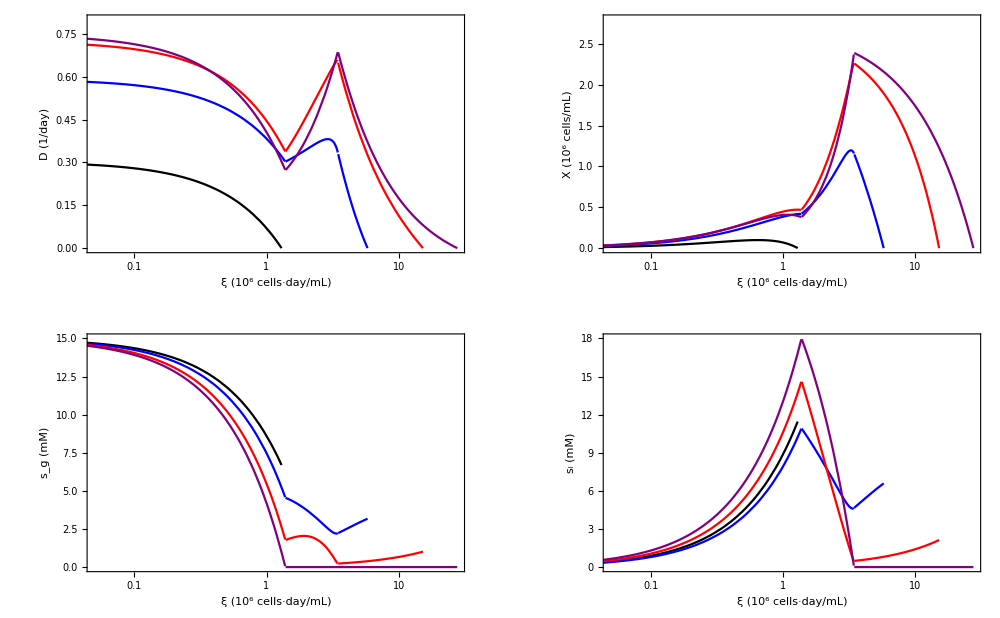

```mathematica
Module[{grid,βlist,colorList,plot,plotopts,ξrange},

βlist={0,1.99 100,1.99 1000,∞};colorList={GrayLevel[0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5]};
plotopts={PlotRange->Full,Frame->True,LabelStyle->Directive[GrayLevel[0],12],FrameStyle->GrayLevel[0],GridLines->None,Axes->None};
ξrange={-3,Log[ξmax[∞]ξunit]};
grid=GraphicsGrid[{
{Show[Table[LogLinearPlot[Deq[βlist⟦i⟧,ξ/ξunit]24,{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","D (1/day)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,0.8}}],
Show[Table[LogLinearPlot[Xeq[βlist⟦i⟧,ξ/ξunit]1.111111,{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","X (10^6 cells/mL)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,2.8}}]},
{Show[Table[LogLinearPlot[sgeq[βlist⟦i⟧,ξ/ξunit],{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","s_g (mM)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,15}}],
Show[Table[LogLinearPlot[sleq[βlist⟦i⟧,ξ/ξunit],{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","s_l (mM)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,18}}]}},
ImageSize->1000];
plot=Legended[grid,LineLegend[colorList,Table["λ_mβ = "<>ToString@NumberForm[N[β vatpmax[0]y],2],{β,βlist}]]];plot]
```

# Polytope

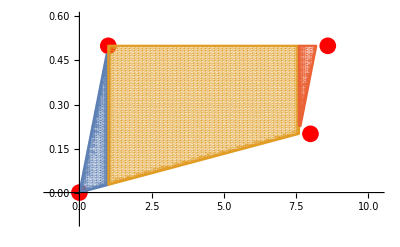

```mathematica
Module[{ξ=0.01,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-1,1.2vatpmax[ξ]},{-0.1,1.2Mg[ξ]}}],
RegionPlot[{polytope1[ξ][vg,vatp]==1,polytope2[ξ][vg,vatp]==1,polytope3[ξ][vg,vatp]==1,polytope4[ξ][vg,vatp]==1},{vatp,0,vatpmax[ξ]},{vg,0,Mg[ξ]},PlotPoints->60,MaxRecursion->5]]]
```